## Definitions

Numerical values of constants

```mathematica
nf=5; (* number of flavours *)
ΛQCD=0.217; (* QCD scale in GeV *)
Nc=3; (* colour number *)
b0=2 ⅇ^-EulerGamma; (* dimensionless *)
btmax=1.5; (* impact parameter in GeV^-1 delimiting the perturbative and nonperturbative domains *)
Tf=1/2; (* normalisation of the SU(3) generators *)
```

Scales and coupling

```mathematica
αs[μ_]:=(4π)/((11-2/3 nf)Log[μ^2/ΛQCD^2]);
```

```mathematica
bc[bt_,Q_]:=√(bt^2+(b0/Q)^2);
```

```mathematica
btbar[bt_,Q_]:=√((bt^2+(b0/Q)^2)/(1+(bt/btmax)^2+(b0/(Q btmax))^2));
```

```mathematica
μbar[bt_,Q_]:=b0/btbar[bt,Q];
```

Collinear PDF from MSTW2008   (the xf function takes 4 arguments : xf[set,x,μ,parton_type], parton_type=0 for gluon, set=0 for central set)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/scarpaflorent/Bureau

```mathematica
(* <<"MSTW2008/mstw2008code/mstwpdf.m"; *)
```

```mathematica
(* ReadPDFGrid["MSTW2008/Grids/mstw2008lo",0] *)
```

```mathematica
<<"mstw2008code/mstwpdf.m";
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
ParallelEvaluate[<<"mstw2008code/mstwpdf.m"];
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

«13 more identical outputs»

```mathematica
ReadPDFGrid["Grids/mstw2008lo",0]
```

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
ParallelEvaluate[ReadPDFGrid["Grids/mstw2008lo",0]];
```

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

«13 more identical outputs»

```mathematica
gMSTW[x_,μ_]:=xf[0,x,μ,0]/x;
```

Perturbative Sudakov factor     μ2=μ^2 ; μb2=μb^2 ; Q2=Q^2   (Sresult is the analytical result of S)

```mathematica
S[μb_,Q_]:=(Nc/π Integrate[1/μ2 αs[√μ2](Log[Q2/μ2](1+αs[√μ2] 1/(4π)((67-3 π^2-20Tf nf)/9))-(11-2nf/Nc)/6),{μ2,μb2,Q2},Assumptions->{μb2∈Reals,μb2>0,Q2∈Reals,Q2>0,ΛQCD∈Reals,ΛQCD>0,Nc∈Integers,Nc>0,Tf∈Integers,Tf>0,nf∈Integers,nf>0,ΛQCD^2<μb2,μb2<Q2}])/.μb2->μb^2/.μbint2->μbint^2/.Q2->Q^2//FullSimplify;
```

```mathematica
Sresult[μb_,Q_]:=1/(33-2 nf)12 Nc (-Log[Q^2]+Log[μb^2]+((-67+3 π^2+20 nf Tf) Log[Q^2] Log[μb^2/Q^2])/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2]))-2 Log[ΛQCD] Log[Log[Q^2]-2 Log[ΛQCD]]-Log[ΛQCD] Log[1/(-2 Log[ΛQCD]+Log[μb^2])]+1/6 (-11+(2 nf)/Nc) (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[ΛQCD] Log[-2 Log[ΛQCD]+Log[μb^2]]+((-67+3 π^2+20 nf Tf) (2 Log[ΛQCD] (Log[μb^2] (-1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]]))-(4 Log[ΛQCD]^2+Log[Q^2] Log[μb^2]) Log[(-2 Log[ΛQCD]+Log[μb^2])/(Log[Q^2]-2 Log[ΛQCD])]))/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2])));
```

Nonperturbative Sudakov factor and TMD input

```mathematica
Snptune[bt_,Q_,A_]:=A Log[Q] bt^2;
```

Convolution C[f_1^g f_1^g] : the PDF is non-analytical, preventing any analytical integration

```mathematica
qtCf1f1tunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bc[bt,Q],Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1GausPlot[qt_,R2_,x_,Q_]:=qt/(2π R2) ⅇ^(-qt^2/(2R2))gMSTW[x,Q]^2;
```

## q_T-spectrum with uncertainty bands

Computing and plotting  q_T C[f_1^g f_1^g] for Gaussian f_1^gwith <k_T^2> =3.3±0.8 GeV^2 (red curve with grey uncertainty bands), and for evolved f_1^g using S_NP with b_Tlim ∈ [2;8] GeV^-1 (blue band)

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[0.04,0.64,0.1];
{MatrixForm[minlistbtQ12=Table[{qt,Min[Table[qtCf1f1tunebt[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ12=Table[{qt,Max[Table[qtCf1f1tunebt[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

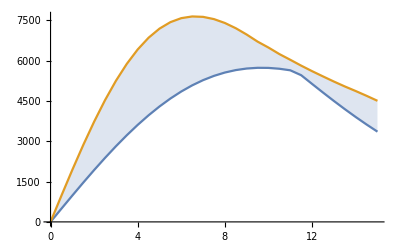
{(0. | 0.
0.5 | 492.611
1. | 981.135
1.5 | 1461.54
2. | 1929.92
2.5 | 2382.55
3. | 2815.92
3.5 | 3226.82
4. | 3612.34
4.5 | 3969.93
5. | 4297.43
5.5 | 4593.09
6. | 4855.55
6.5 | 5083.91
7. | 5277.65
7.5 | 5436.66
8. | 5561.25
8.5 | 5652.06
9. | 5710.08
9.5 | 5736.61
10. | 5733.2
10.5 | 5701.65
11. | 5643.93
11.5 | 5461.17
12. | 5136.85
12.5 | 4816.42
13. | 4502.97
13.5 | 4198.96
14. | 3906.21
14.5 | 3626.02
15. | 3359.25),(0. | 0.
0.5 | 978.537
1. | 1938.28
1.5 | 2861.17
2. | 3730.56
2.5 | 4531.87
3. | 5253.01
3.5 | 5884.72
4. | 6420.69
4.5 | 6857.92
5. | 7195.89
5.5 | 7436.97
6. | 7585.74
6.5 | 7648.66
7. | 7633.57
7.5 | 7549.27
8. | 7405.08
8.5 | 7210.47
9. | 6974.7
9.5 | 6711.73
10. | 6490.43
10.5 | 6247.78
11. | 6035.38
11.5 | 5817.27
12. | 5611.7
12.5 | 5416.78
13. | 5225.13
13.5 | 5043.23
14. | 4872.28
14.5 | 4694.11
15. | 4507.77),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[0.04,0.64,0.1];
{MatrixForm[minlistbtQ30=Table[{qt,Min[Table[qtCf1f1tunebt[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ30=Table[{qt,Max[Table[qtCf1f1tunebt[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

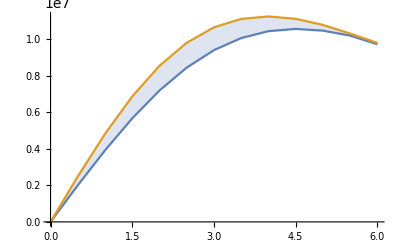
{(0. | 0.
0.5 | 2.00109×10^6
1. | 3.91611×10^6
1.5 | 5.66698×10^6
2. | 7.19029×10^6
2.5 | 8.44194×10^6
3. | 9.39893×10^6
3.5 | 1.00586×10^7
4. | 1.04359×10^7
4.5 | 1.05588×10^7
5. | 1.04636×10^7
5.5 | 1.01907×10^7
6. | 9.71716×10^6),(0. | 0.
0.5 | 2.48442×10^6
1. | 4.81626×10^6
1.5 | 6.86568×10^6
2. | 8.54222×10^6
2.5 | 9.80206×10^6
3. | 1.06454×10^7
3.5 | 1.11063×10^7
4. | 1.12399×10^7
4.5 | 1.11093×10^7
5. | 1.07765×10^7
5.5 | 1.03035×10^7
6. | 9.79293×10^6),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[0.04,0.64,0.1];
{MatrixForm[minlistbtQ12xdm3=Table[{qt,Min[Table[qtCf1f1tunebt[10^-3,12,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ12xdm3=Table[{qt,Max[Table[qtCf1f1tunebt[10^-3,12,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ12xdm3,maxlistbtQ12xdm3},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

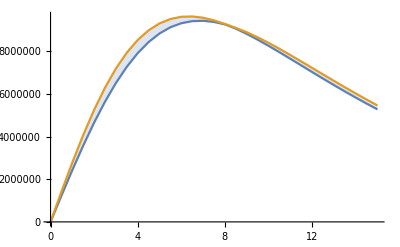
{(0. | 0.
0.5 | 1.22731×10^6
1. | 2.42802×10^6
1.5 | 3.57698×10^6
2. | 4.65186×10^6
2.5 | 5.63412×10^6
3. | 6.50975×10^6
3.5 | 7.26953×10^6
4. | 7.90897×10^6
4.5 | 8.42789×10^6
5. | 8.82981×10^6
5.5 | 9.12119×10^6
6. | 9.31065×10^6
6.5 | 9.4082×10^6
7. | 9.42453×10^6
7.5 | 9.37054×10^6
8. | 9.25682×10^6
8.5 | 9.05792×10^6
9. | 8.81159×10^6
9.5 | 8.54105×10^6
10. | 8.25293×10^6
10.5 | 7.95287×10^6
11. | 7.64561×10^6
11.5 | 7.33508×10^6
12. | 7.02451×10^6
12.5 | 6.7165×10^6
13. | 6.41311×10^6
13.5 | 6.116×10^6
14. | 5.82645×10^6
14.5 | 5.54538×10^6
15. | 5.27352×10^6),(0. | 0.
0.5 | 1.41213×10^6
1. | 2.78206×10^6
1.5 | 4.07143×10^6
2. | 5.2489×10^6
2.5 | 6.292×10^6
3. | 7.18764×10^6
3.5 | 7.93138×10^6
4. | 8.52587×10^6
4.5 | 8.97904×10^6
5. | 9.30223×10^6
5.5 | 9.50874×10^6
6. | 9.61261×10^6
6.5 | 9.62791×10^6
7. | 9.5681×10^6
7.5 | 9.44575×10^6
8. | 9.27846×10^6
8.5 | 9.09383×10^6
9. | 8.8895×10^6
9.5 | 8.65346×10^6
10. | 8.39268×10^6
10.5 | 8.11361×10^6
11. | 7.82181×10^6
11.5 | 7.52201×10^6
12. | 7.21816×10^6
12.5 | 6.91358×10^6
13. | 6.61092×10^6
13.5 | 6.31238×10^6
14. | 6.0197×10^6
14.5 | 5.73418×10^6
15. | 5.45688×10^6),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[0.04,0.64,0.1];
{MatrixForm[minlistbtQ30xdm3=Table[{qt,Min[Table[qtCf1f1tunebt[10^-3,30,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ30xdm3=Table[{qt,Max[Table[qtCf1f1tunebt[10^-3,30,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ30xdm3,maxlistbtQ30xdm3},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

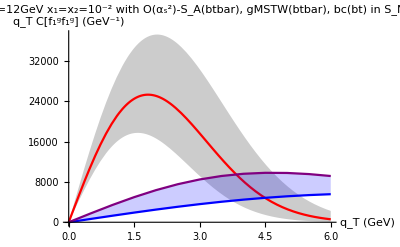
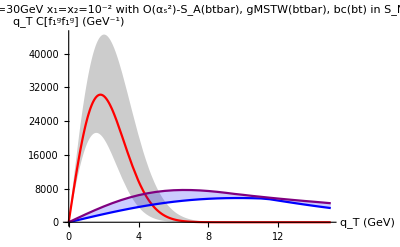

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2 with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2 with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP"]}
```

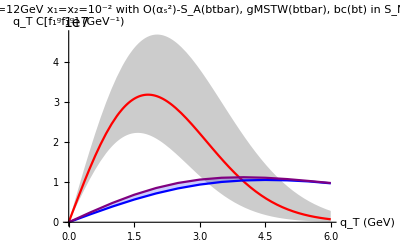
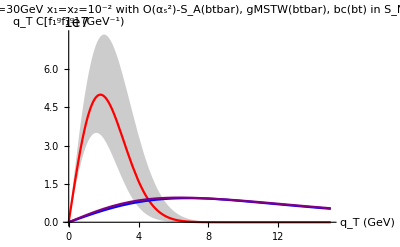

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-3,12]],qtCf1f1GausPlot[qt,3.3,10^-3,12],Max[qtCf1f1GausPlot[qt,R2,10^-3,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12xdm3,maxlistbtQ12xdm3},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2 with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-3,30]],qtCf1f1GausPlot[qt,3.3,10^-3,30],Max[qtCf1f1GausPlot[qt,R2,10^-3,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30xdm3,maxlistbtQ30xdm3},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2 with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP"]}
```

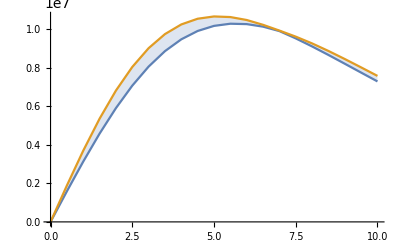
{(0. | 0.
0.5 | 1.58831×10^6
1. | 3.12979×10^6
1.5 | 4.58089×10^6
2. | 5.90414×10^6
2.5 | 7.07029×10^6
3. | 8.05952×10^6
3.5 | 8.86172×10^6
4. | 9.47581×10^6
4.5 | 9.90847×10^6
5. | 1.01725×10^7
5.5 | 1.02848×10^7
6. | 1.0265×10^7
6.5 | 1.01334×10^7
7. | 9.90349×10^6
7.5 | 9.52416×10^6
8. | 9.10647×10^6
8.5 | 8.66415×10^6
9. | 8.20847×10^6
9.5 | 7.74835×10^6
10. | 7.29086×10^6),(0. | 0.
0.5 | 1.88664×10^6
1. | 3.69493×10^6
1.5 | 5.35552×10^6
2. | 6.81502×10^6
2.5 | 8.03974×10^6
3. | 9.01584×10^6
3.5 | 9.74658×10^6
4. | 1.0248×10^7
4.5 | 1.05439×10^7
5. | 1.0662×10^7
5.5 | 1.06309×10^7
6. | 1.04778×10^7
6.5 | 1.02279×10^7
7. | 9.92894×10^6
7.5 | 9.61421×10^6
8. | 9.26291×10^6
8.5 | 8.87144×10^6
9. | 8.45292×10^6
9.5 | 8.01832×10^6
10. | 7.57671×10^6),-Graphics-}

```mathematica
qtlist=Range[0,10,0.5];
Alist=Range[0.04,0.64,0.1];
{MatrixForm[minlistbtQ20xdm3=Table[{qt,Min[Table[qtCf1f1tunebt[10^-3,20,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ20xdm3=Table[{qt,Max[Table[qtCf1f1tunebt[10^-3,20,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ20xdm3,maxlistbtQ20xdm3},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
MatrixForm[listnonevQ12=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6,0.1}]]];
```

```mathematica
MatrixForm[listnonevQ30=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15,0.1}]]];
```

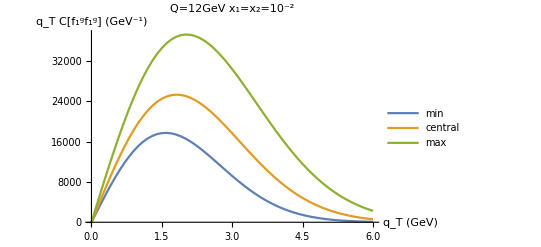
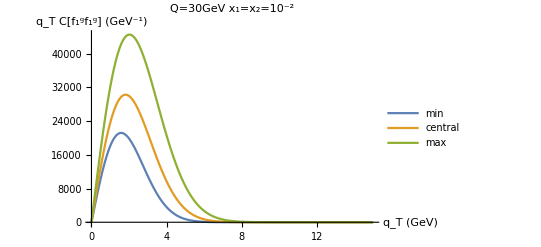

```mathematica
{ListPlot[{listnonevQ12[[All,{1,2}]],listnonevQ12[[All,{1,3}]],listnonevQ12[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],
ListPlot[{listnonevQ30[[All,{1,2}]],listnonevQ30[[All,{1,3}]],listnonevQ30[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
MatrixForm[listnonevQ12xdm3=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-3,12]],qtCf1f1GausPlot[qt,3.3,10^-3,12],Max[qtCf1f1GausPlot[qt,R2,10^-3,12]]},{qt,0,6,0.1}]]];
```

```mathematica
MatrixForm[listnonevQ30xdm3=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-3,30]],qtCf1f1GausPlot[qt,3.3,10^-3,30],Max[qtCf1f1GausPlot[qt,R2,10^-3,30]]},{qt,0,15,0.1}]]];
```

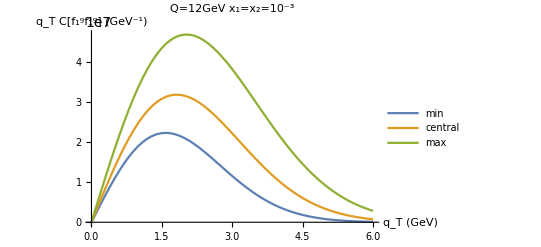
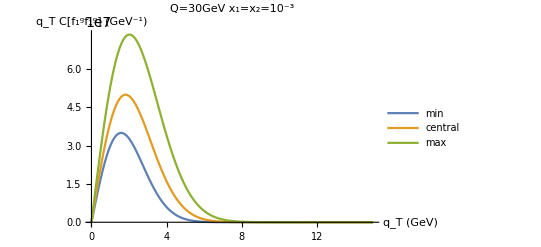

```mathematica
{ListPlot[{listnonevQ12xdm3[[All,{1,2}]],listnonevQ12xdm3[[All,{1,3}]],listnonevQ12xdm3[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=12GeV x_1=x_2=10^-3"],
ListPlot[{listnonevQ30xdm3[[All,{1,2}]],listnonevQ30xdm3[[All,{1,3}]],listnonevQ30xdm3[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=30GeV x_1=x_2=10^-3"]}
```

Exporting values for the q_T C[f_1^g f_1^g] plots

```mathematica
Export["qtCf1f1nonevboundsQ12.dat",listnonevQ12];
Export["qtCf1f1nonevboundsQ30.dat",listnonevQ30];
Export["qtCf1f1SnptuneboundsQ12.dat",Transpose[{minlistbtQ12[[All,1]],minlistbtQ12[[All,2]],maxlistbtQ12[[All,2]]}]];
Export["qtCf1f1SnptuneboundsQ30.dat",Transpose[{minlistbtQ30[[All,1]],minlistbtQ30[[All,2]],maxlistbtQ30[[All,2]]}]];
```

```mathematica
Export["qtCf1f1nonevboundsQ12xdm3.dat",listnonevQ12xdm3];
Export["qtCf1f1nonevboundsQ30xdm3.dat",listnonevQ30xdm3];
```

```mathematica
Export["qtCf1f1SnptuneboundsQ12xdm3.dat",Transpose[{minlistbtQ12xdm3[[All,1]],minlistbtQ12xdm3[[All,2]],maxlistbtQ12xdm3[[All,2]]}]];
Export["qtCf1f1SnptuneboundsQ30xdm3.dat",Transpose[{minlistbtQ30xdm3[[All,1]],minlistbtQ30xdm3[[All,2]],maxlistbtQ30xdm3[[All,2]]}]];
```

```mathematica
Export["qtCf1f1SnptuneboundsQ20xdm3.dat",Transpose[{minlistbtQ20xdm3[[All,1]],minlistbtQ20xdm3[[All,2]],maxlistbtQ20xdm3[[All,2]]}]];
```

## Normalised q_T-spectrum : evol VS. non-evol VS. LHCb data at Q=8GeV

```mathematica
qtCf1f1Norm[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bc[bt,Q],Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bc[bt,Q],Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NormnoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1GausNorm[qt_,R2_,Q_]:=-(ⅇ^(-qt^2/(2 R2)) qt)/((-1+ⅇ^(-Q^2/(8 R2))) R2);
```

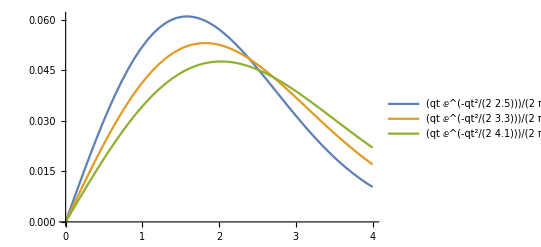

```mathematica
Plot[{qt/(2π *2.5) ⅇ^(-qt^2/(2*2.5)),qt/(2π *3.3) ⅇ^(-qt^2/(2*3.3)),qt/(2π *4.1) ⅇ^(-qt^2/(2*4.1))},{qt,0,4},PlotLegends->"Expressions"]
```

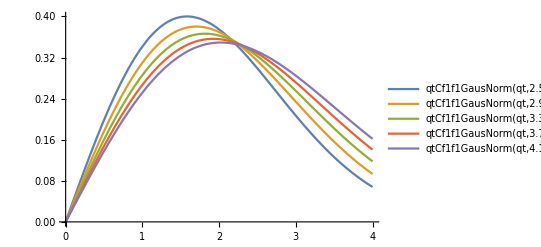

```mathematica
Plot[{qtCf1f1GausNorm[qt,2.5,8],qtCf1f1GausNorm[qt,2.9,8],qtCf1f1GausNorm[qt,3.3,8],qtCf1f1GausNorm[qt,3.7,8],qtCf1f1GausNorm[qt,4.1,8]},{qt,0,4},PlotLegends->"Expressions"]
```

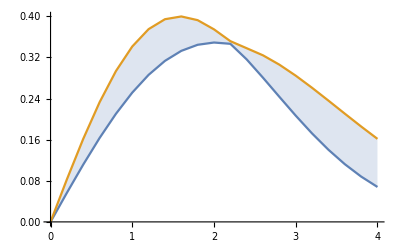
{(0. | 0.
0.2 | 0.0565837
0.4 | 0.111523
0.6 | 0.163254
0.8 | 0.210365
1. | 0.251662
1.2 | 0.286217
1.4 | 0.313401
1.6 | 0.332901
1.8 | 0.344709
2. | 0.349107
2.2 | 0.346627
2.4 | 0.316255
2.6 | 0.280505
2.8 | 0.243399
3. | 0.206788
3.2 | 0.172127
3.4 | 0.140451
3.6 | 0.112394
3.8 | 0.0882419
4. | 0.067991),(0. | 0.
0.2 | 0.082735
0.4 | 0.161546
0.6 | 0.232818
0.8 | 0.293518
1. | 0.341409
1.2 | 0.375179
1.4 | 0.394474
1.6 | 0.399848
1.8 | 0.39263
2. | 0.374738
2.2 | 0.351774
2.4 | 0.338007
2.6 | 0.324134
2.8 | 0.305992
3. | 0.284601
3.2 | 0.26097
3.4 | 0.236053
3.6 | 0.21071
3.8 | 0.185687
4. | 0.161598),-Graphics-}

```mathematica
qtlist=Range[0,4,0.2];
R2list=Range[2.5,4.1,0.01];
Tabltg=Map[Table[qtCf1f1GausNorm[#,R2,8],{R2,R2list}]&,qtlist];
{MatrixForm[mintgQ8=Map[{qtlist[[#]],Min[Tabltg[[#]]]}&,Range[Length[qtlist]]]],MatrixForm[maxtgQ8=Map[{qtlist[[#]],Max[Tabltg[[#]]]}&,Range[Length[qtlist]]]],ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

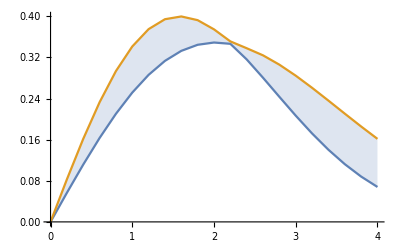
{(0. | 0.
0.2 | 0.0565837
0.4 | 0.111523
0.6 | 0.163254
0.8 | 0.210365
1. | 0.251662
1.2 | 0.286217
1.4 | 0.313401
1.6 | 0.332901
1.8 | 0.344709
2. | 0.349107
2.2 | 0.346627
2.4 | 0.316255
2.6 | 0.280505
2.8 | 0.243399
3. | 0.206788
3.2 | 0.172127
3.4 | 0.140451
3.6 | 0.112394
3.8 | 0.0882419
4. | 0.067991),(0. | 0.
0.2 | 0.082735
0.4 | 0.161546
0.6 | 0.232818
0.8 | 0.293518
1. | 0.341409
1.2 | 0.375179
1.4 | 0.394474
1.6 | 0.399848
1.8 | 0.39263
2. | 0.374738
2.2 | 0.35131
2.4 | 0.338007
2.6 | 0.324134
2.8 | 0.305992
3. | 0.284601
3.2 | 0.26097
3.4 | 0.236053
3.6 | 0.21071
3.8 | 0.185687
4. | 0.161598),-Graphics-}

```mathematica
qtlist=Range[0,4,0.2];
R2list=Range[2.5,4.1,0.8];
Tabltg=Map[Table[qtCf1f1GausNorm[#,R2,8],{R2,R2list}]&,qtlist];
{MatrixForm[mintgQ8=Map[{qtlist[[#]],Min[Tabltg[[#]]]}&,Range[Length[qtlist]]]],MatrixForm[maxtgQ8=Map[{qtlist[[#]],Max[Tabltg[[#]]]}&,Range[Length[qtlist]]]],ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
qtlist=Range[0,4,0.2];
listtgQ8=Map[{mintgQ8[[#,1]],mintgQ8[[#,2]],qtCf1f1GausNorm[qtlist[[#]],3.3,8],maxtgQ8[[#,2]]}&,Range[Length[mintgQ8[[All,1]]]]];
```

```mathematica
Export["qtCf1f1nonevNormQ8.dat",listtgQ8];
```

!!! WATCH OUT: using the method with Interval[ ] replaces R2 in the Min[ ] (or Max[ ]) function by the interval and not a fixed value, allowing it to try different values for each occurrence of the same argument inside the tested function when searching for the minimum (or maximum). Such a method is therefore doing wrong, allowing for much more possibilities than there are in reality.

```mathematica
With[{x=Interval[1,2]},Max[ⅇ^x+ⅇ^-x]]
```

1/ⅇ+ⅇ^2

```mathematica
With[{R2=Interval[2.5,4.1]},Min[qtCf1f1GausNorm[0.2,R2,8]]]
```

0.0504482

```mathematica
With[{R2=Interval[3.3+0.8{-1,1}]},Min[qtCf1f1GausNorm[2.4,R2,8]]]
```

0.192839

```mathematica
qtlist=Range[0,4,0.2];
Alist={0.04,0.16,0.64};
Tabltest=ParallelMap[Table[qtCf1f1Norm[10^-2,8,#,A],{A,Alist}]&,qtlist];
```

```mathematica
Tablbc1=Table[{qt,qtCf1f1Norm[10^-2,8,qt,2]},{qt,qtlist}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.207487}. NIntegrate obtained 25259.6 and 0.0278237 for the integral and error estimates.

```mathematica
Tablbc2
```

{{0.,0.},{0.2,0.0371478},{0.4,0.0737982},{0.6,0.109466},{0.8,0.143692},{1.,0.176053},{1.2,0.206174},{1.4,0.233732},{1.6,0.258468},{1.8,0.280186},{2.,0.298755},{2.2,0.31411},{2.4,0.32625},{2.6,0.335228},{2.8,0.341152},{3.,0.344176},{3.2,0.344489},{3.4,0.342309},{3.6,0.337877},{3.8,0.331446},{4.,0.323275}}

```mathematica
Tabltestb=Transpose[{qtlist,Tablbc1[[All,2]],Tabltest[[All,1]],Tabltest[[All,2]],Tabltest[[All,3]]}];
```

```mathematica
Tabltestb//MatrixForm
```

(0. | 0. | 0. | 0. | 0.
0.2 | 0.0317689 | 0.0317689 | 0.0292354 | 0.0274785
0.4 | 0.0632963 | 0.0632963 | 0.058329 | 0.0548775
0.6 | 0.0943439 | 0.0943439 | 0.0871399 | 0.0821178
0.8 | 0.12468 | 0.12468 | 0.11553 | 0.109121
1. | 0.154082 | 0.154082 | 0.143364 | 0.13581
1.2 | 0.18234 | 0.18234 | 0.170511 | 0.162109
1.4 | 0.209259 | 0.209259 | 0.196848 | 0.187945
1.6 | 0.234661 | 0.234661 | 0.222255 | 0.213244
1.8 | 0.258389 | 0.258389 | 0.246621 | 0.237937
2. | 0.280304 | 0.280304 | 0.269845 | 0.261963
2.2 | 0.300292 | 0.300292 | 0.291832 | 0.285252
2.4 | 0.318261 | 0.318261 | 0.312499 | 0.307748
2.6 | 0.334141 | 0.334141 | 0.33177 | 0.329394
2.8 | 0.347889 | 0.347889 | 0.349584 | 0.350137
3. | 0.359482 | 0.359482 | 0.365886 | 0.369929
3.2 | 0.368922 | 0.368922 | 0.380636 | 0.388726
3.4 | 0.37623 | 0.37623 | 0.393802 | 0.406489
3.6 | 0.381449 | 0.381449 | 0.40536 | 0.423183
3.8 | 0.38464 | 0.38464 | 0.415312 | 0.438778
4. | 0.385881 | 0.385881 | 0.423649 | 0.453247)

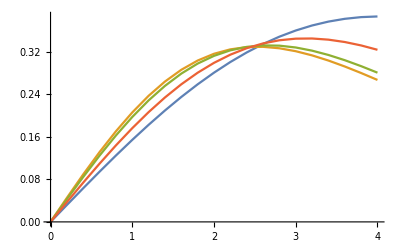

```mathematica
ListPlot[{Tabltestb[[All,{1,2}]],Tabltestb[[All,{1,3}]],Tabltestb[[All,{1,4}]],Tabltestb[[All,{1,5}]]},Joined->True]
```

```mathematica
qtlist=Range[0,4,0.2];
Alist={2,4,8};
Tabltest2=ParallelMap[Table[qtCf1f1tunebt[10^-2,8,#,A],{A,Alist}]&,qtlist];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.207487}. NIntegrate obtained 25259.6 and 0.0278237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.207487}. NIntegrate obtained 15344.7 and 0.0209689 for the integral and error estimates.

```mathematica
qtlist=Range[0,4,0.2];
Alist=Range[2,8,1];
MatrixForm[Tabl8test=ParallelMap[Table[#+A,{A,Alist}]&,qtlist]]
```

(2. | 3. | 4. | 5. | 6. | 7. | 8.
2.2 | 3.2 | 4.2 | 5.2 | 6.2 | 7.2 | 8.2
2.4 | 3.4 | 4.4 | 5.4 | 6.4 | 7.4 | 8.4
2.6 | 3.6 | 4.6 | 5.6 | 6.6 | 7.6 | 8.6
2.8 | 3.8 | 4.8 | 5.8 | 6.8 | 7.8 | 8.8
3. | 4. | 5. | 6. | 7. | 8. | 9.
3.2 | 4.2 | 5.2 | 6.2 | 7.2 | 8.2 | 9.2
3.4 | 4.4 | 5.4 | 6.4 | 7.4 | 8.4 | 9.4
3.6 | 4.6 | 5.6 | 6.6 | 7.6 | 8.6 | 9.6
3.8 | 4.8 | 5.8 | 6.8 | 7.8 | 8.8 | 9.8
4. | 5. | 6. | 7. | 8. | 9. | 10.
4.2 | 5.2 | 6.2 | 7.2 | 8.2 | 9.2 | 10.2
4.4 | 5.4 | 6.4 | 7.4 | 8.4 | 9.4 | 10.4
4.6 | 5.6 | 6.6 | 7.6 | 8.6 | 9.6 | 10.6
4.8 | 5.8 | 6.8 | 7.8 | 8.8 | 9.8 | 10.8
5. | 6. | 7. | 8. | 9. | 10. | 11.
5.2 | 6.2 | 7.2 | 8.2 | 9.2 | 10.2 | 11.2
5.4 | 6.4 | 7.4 | 8.4 | 9.4 | 10.4 | 11.4
5.6 | 6.6 | 7.6 | 8.6 | 9.6 | 10.6 | 11.6
5.8 | 6.8 | 7.8 | 8.8 | 9.8 | 10.8 | 11.8
6. | 7. | 8. | 9. | 10. | 11. | 12.)

```mathematica
MatrixForm[minlisttest=Map[{qtlist[[#]],Min[Tabl8test[[#]]]}&,Range[Length[qtlist]]]]
```

(0. | 2.
0.2 | 2.2
0.4 | 2.4
0.6 | 2.6
0.8 | 2.8
1. | 3.
1.2 | 3.2
1.4 | 3.4
1.6 | 3.6
1.8 | 3.8
2. | 4.
2.2 | 4.2
2.4 | 4.4
2.6 | 4.6
2.8 | 4.8
3. | 5.
3.2 | 5.2
3.4 | 5.4
3.6 | 5.6
3.8 | 5.8
4. | 6.)

```mathematica
qtlist=Range[0,4,0.2];
Alist=Range[0.04,0.64,0.1];
Tabl8=ParallelMap[Table[qtCf1f1Norm[10^-2,8,#,A],{A,Alist}]&,qtlist];
```

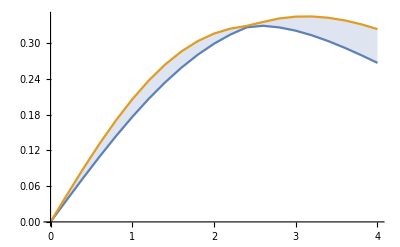
{(0. | 0.
0.2 | 0.0371478
0.4 | 0.0737982
0.6 | 0.109466
0.8 | 0.143692
1. | 0.176053
1.2 | 0.206174
1.4 | 0.233732
1.6 | 0.258468
1.8 | 0.280186
2. | 0.298755
2.2 | 0.31411
2.4 | 0.32625
2.6 | 0.328839
2.8 | 0.326119
3. | 0.320611
3.2 | 0.31278
3.4 | 0.303072
3.6 | 0.291904
3.8 | 0.279654
4. | 0.26665),(0. | 0.
0.2 | 0.0451855
0.4 | 0.0892465
0.6 | 0.131187
0.8 | 0.170187
1. | 0.205581
1.2 | 0.236849
1.4 | 0.263626
1.6 | 0.285711
1.8 | 0.30306
2. | 0.315777
2.2 | 0.324084
2.4 | 0.328709
2.6 | 0.335228
2.8 | 0.341152
3. | 0.344176
3.2 | 0.344489
3.4 | 0.342309
3.6 | 0.337877
3.8 | 0.331446
4. | 0.323275),-Graphics-}

```mathematica
{MatrixForm[minlistbtNormQ8=Map[{qtlist[[#]],Min[Tabl8[[#]]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtNormQ8=Map[{qtlist[[#]],Max[Tabl8[[#]]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtNormQ8,maxlistbtNormQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

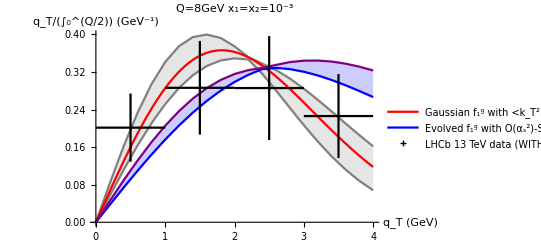

```mathematica
Show[
      ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},Joined->True,FillingStyle->Darker,PlotStyle->{Gray,Gray}],

Plot[qtCf1f1GausNorm[qt,3.3,8],{qt,0,4},PlotLegends->{"Gaussian f_1^g with <k_T^2>=3.3±0.8 GeV^2"},PlotStyle->Red],

         ListPlot[{minlistbtNormQ8,maxlistbtNormQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple},PlotLegends->{"Evolved f_1^g with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP with b_Tlim ∈ [2;8] GeV^-1"}],

         ErrorListPlot[LHCb13datNODPSPlot4[[1;;4]],PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],
      AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-3",PlotRange->All]
```

```mathematica
qtlist=Range[0,4,0.2];
Tabl8noSnp=ParallelMap[{#,qtCf1f1NormnoSnp[10^-2,8,#]}&,qtlist];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.21927639100886×10^55895 and 8.21927639100886×10^55895 for the integral and error estimates.

```mathematica
Tabl8noSnp
```

{{0.,0.},{0.2,0.0462532},{0.4,0.0911186},{0.6,0.133715},{0.8,0.173188},{1.,0.208829},{1.2,0.240105},{1.4,0.266659},{1.6,0.288317},{1.8,0.305073},{2.,0.317069},{2.2,0.324572},{2.4,0.327954},{2.6,0.327645},{2.8,0.324124},{3.,0.317885},{3.2,0.309414},{3.4,0.299174},{3.6,0.287589},{3.8,0.275034},{4.,0.261836}}

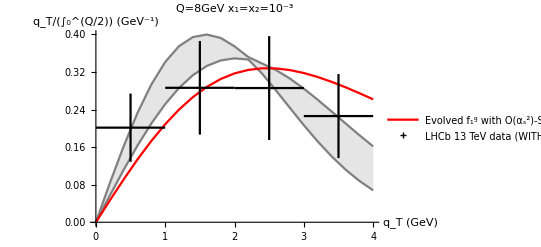

```mathematica
Show[
      ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},Joined->True,FillingStyle->Darker,PlotStyle->{Gray,Gray}],

 ListPlot[Tabl8noSnp,Joined->True,PlotStyle->Red,PlotLegends->{"Evolved f_1^g with O(α_s^2)-S_A(b_T^*(b_c(b_T))) and no S_NP"}],

         ErrorListPlot[LHCb13datNODPSPlot4[[1;;4]],PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],
      AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-3",PlotRange->All]
```

!!! WATCH OUT: using the method with Interval[ ] replaces R2 in the Min[ ] (or Max[ ]) function by the interval and not a fixed value, allowing it to try different values for each occurrence of the same argument inside the tested function when searching for the minimum (or maximum). Such a method is therefore doing wrong, allowing for much more possibilities than there are in reality.

```mathematica
MatrixForm[listnonevNormQ8=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausNorm[qt,R2,8]],qtCf1f1GausNorm[qt,3.3,8],Max[qtCf1f1GausNorm[qt,R2,8]]},{qt,0,4,0.2}]]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
LHCb13datNODPSPlot4=({{{0.5,0.20153314163536068}, ErrorBar[0.5,0.07264702241987869]}, {{1.5,0.28638454718535394}, ErrorBar[0.5,0.09971493099591708]}, {{2.5,0.28588343844213565}, ErrorBar[0.5,0.11058447437610346]}, {{3.5,0.22619887273714984}, ErrorBar[0.5,0.08949827380291174]}, {{4.5,0.17368752642040558}, ErrorBar[0.5,0.07678015530360593]}, {{5.5,0.09273362664484106}, ErrorBar[0.5,0.05181906106834104]}, {{6.5,0.10962524347918191}, ErrorBar[0.5,0.042881199279617664]}, {{7.5,0.060524634528971465}, ErrorBar[0.5,0.03721473022552986]}});
```

!!! WATCH OUT: using the method with Interval[ ] replaces R2 in the Min[ ] (or Max[ ]) function by the interval and not a fixed value, allowing it to try different values for each occurrence of the same argument inside the tested function when searching for the minimum (or maximum). Such a method is therefore doing wrong, allowing for much more possibilities than there are in reality.

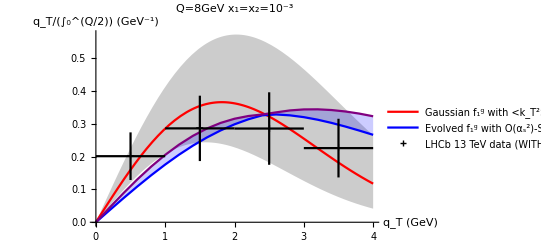

```mathematica
Show[With[{R2=Interval[3.3+0.8{-1,1}]},
      Plot[{Min[qtCf1f1GausNorm[qt,R2,8]],qtCf1f1GausNorm[qt,3.3,8],Max[qtCf1f1GausNorm[qt,R2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","Gaussian f_1^g with <k_T^2>=3.3±0.8 GeV^2",""}]
                ],
         ListPlot[{minlistbtNormQ8,maxlistbtNormQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple},PlotLegends->{"Evolved f_1^g with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP with b_Tlim ∈ [2;8] GeV^-1"}],
         ErrorListPlot[LHCb13datNODPSPlot4[[1;;4]],PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],
      AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-3",PlotRange->All]
```

```mathematica
Export["qtCf1f1NormQ8.dat",Transpose[{minlistbtNormQ8[[All,1]],minlistbtNormQ8[[All,2]],maxlistbtNormQ8[[All,2]]}]];
```